# Implementations, approximations and computational bounds

## k Interesting Paths Approximation Implementation

### First, instantiate the functions.

Functions:

```mathematica
Clear[explore,kIPApprox,kIPExact]
explore[g_,k_,path_]:=If[k<=1,
Table[Append[path ,lastEdge],{lastEdge,EdgeList[g,path[[-1,2]]->{"e",_}]}],
Flatten[Table[explore[g,k-1,Append[path ,edge]],{edge,EdgeList[g,path[[-1,2]]->{Except["e"],_}]}],1]
]
kIPExact[g_,levels_,k_]:=(*Initializer for exact solving*)
Module[{allPaths=Flatten[Table[Table[explore[g,k+1,{edge}],{edge,EdgeList[g,{"b",l}->{Except["e"],_}]}],{l,1,levels-k}],2][[All,2;;-2]],reference,b,exactSolve},
exactSolve[remainingPaths_,solution_]:=If[ValueQ[kIPExact[solution],Method->"TrialEvaluation"],solution,If[remainingPaths=={},(*Recursion for exact solving*)
exactSolve[solution]=1;
{Length@solution},
If[solution=={},
Flatten[Table[exactSolve[Select[remainingPaths,Times@@(p-#)!=0& ],Sort@p],{p,remainingPaths}],1],Flatten[Table[exactSolve[Select[remainingPaths,Times@@(p-#)!=0& ],Sort@Join[solution,p]],{p,remainingPaths}],1]]
]];
Print[AbsoluteTiming[Flatten[Table[Table[explore[g,k+1,{edge}],{edge,EdgeList[g,{"b",l}->{Except["e"],_}]}],{l,1,levels-k}],2][[All,2;;-2]]][[1]]];
reference=DeleteDuplicates[Flatten[allPaths]];
b=Table[Flatten[Table[Position[reference,edge][[1]],{edge,path}]],{path,allPaths}];
Print[AbsoluteTiming[Max[exactSolve[b,{}]]/k][[1]]];
Max[exactSolve[b,{}]]/k
]
Clear[graphGen,kIPApprox]
graphGen[verticesL_,edgesL_]:=Module[{(*Random Graph Generation*)
i,edges=Join[Flatten[Table[Table[{"b",l}->{l,i},{i,1,verticesL[[l]]}],{l,1,Length[verticesL]}],1],Flatten[Table[Table [{l,i}->{"e",l},{i,1,verticesL[[l]]}],{l,1,Length[verticesL]}],1],Flatten[Table[RandomSample[Flatten[Table[{l,i}->{l+1,j},{i,1,verticesL[[l]]},{j,1,verticesL[[l+1]]}],1],edgesL[[l]]],{l,1,Length[edgesL]}],1]]},
Graph[edges]
];
kIPApprox[g_,levels_,k_]:=Module[{(*Approximation *)
vL=VertexList[g],capacity,costs,mx,mx2,updates,newCostWithExtraEdges,newCosts,i,newGraph,flow,allPaths,solution,selectionList,filteredUpdates,edges=EdgeList[g],newG},
costs=Table[0,Length[edges]];
capacity=Join[Table[Length[vL],2(Length[vL]-2levels)],Table[1,Length[edges]-2(Length[vL]-2levels)]];
mx=Sum[FindMinimumCostFlow[g,{"b",l},{"e",l+k},"FlowMatrix"],{l,1,levels-k}];
updates=Select[Flatten[Table[{i,j},{i,1 ,Length[vL]},{j,1 ,Length[vL]}],1],Part[mx,Sequence@@#]!=0&];
newCostWithExtraEdges=Table[vL[[i[[1]]]]->vL[[i[[2]]]]->mx[[Sequence@@i]],{i,updates}];
filteredUpdates=Select[newCostWithExtraEdges,#[[1,1,1]]!= "b"&&#[[1,2,1]]!="e"&];
newCosts=Merge[{Association[Thread[edges->costs]],filteredUpdates},Total];(*Print[{Length[vL],Length[edges],Length[capacity],Length[newCosts]}];*)
newG=Graph[edges,EdgeCapacity->capacity,EdgeCost->Values[newCosts]]; (*Round 2*)
mx2=Sum[FindMinimumCostFlow[newG,{"b",l},{"e",l+k},"FlowMatrix"],{l,1,levels-k}];
updates=Select[Flatten[Table[{i,j},{i,1 ,Length[vL]},{j,1 ,Length[vL]}],1],Part[mx2,Sequence@@#]!=0&];
newCostWithExtraEdges=Table[vL[[i[[1]]]]->vL[[i[[2]]]]->mx2[[Sequence@@i]],{i,updates}];
newCosts=Merge[{Association[Thread[EdgeList[newG]->costs]],filteredUpdates},Total];
flow=Association@newCostWithExtraEdges;
newGraph=Graph[Keys[flow]];
allPaths=Flatten[Table[Table[explore[newGraph,k+1,{edge}],{edge,EdgeList[newGraph,{"b",l}->{Except["e"],_}]}],{l,1,7-k}],2];
solution={};
selectionList=Sort@Association@Table[path->Sum[flow[e],{e,path}],{path,allPaths}];
AppendTo[solution,Normal[selectionList][[1]]];
selectionList=Select[Normal@selectionList,Intersection[solution[[-1,1]],#[[1,2;;-2]]]=={}&];
While[selectionList!={},
AppendTo[solution,Normal[selectionList][[1]]];
selectionList=Select[Normal@selectionList,Intersection[solution[[-1,1]],#[[1,2;;-2]]]=={}&];
];
If[solution=={},{},solution[[All,1]]]
]
```

### Second, generate the graph. This includes sink and source nodes.

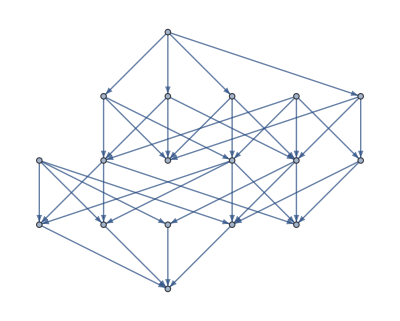

```mathematica
g=graphGen[{4,4,4},{8,8}]
```

### Third, find the approximate solution.

This may be a much larger graph if desired. Take the length of the solution to know the size.

```mathematica
g=graphGen[{4,4,4,5,5},{8,8,15,10}]
kIPApprox[g,3,2]
Length@%
```

{{{b,1}->{1,4},{1,4}->{2,4},{2,4}->{3,2},{3,2}->{e,3}},{{b,1}->{1,3},{1,3}->{2,1},{2,1}->{3,3},{3,3}->{e,3}},{{b,1}->{1,3},{1,3}->{2,3},{2,3}->{3,1},{3,1}->{e,3}},{{b,1}->{1,2},{1,2}->{2,2},{2,2}->{3,1},{3,1}->{e,3}},{{b,1}->{1,2},{1,2}->{2,3},{2,3}->{3,4},{3,4}->{e,3}}}

5

### Fourth, find the exact solution.

This needs to be a small graph. To ease computation, it only returns the maximal number of disjoint k paths.

```mathematica
Now[]
```

Mon 28 Nov 2022 23:35:18GMT-5[]

```mathematica
g=graphGen[{4,4,4},{8,8}];
```

```mathematica
g=graphGen[{4,4,4,3},{8,8,8}];
kIPExact[g,3,2]
```

0.0006638

0.0368083

4

```mathematica
ValueQ[kIPExact[g,3,2],Method->"TrialEvaluation"]
```

True

### Fifth, the average case. (smaller graph)

Test the average case.

```mathematica
Clear[averageCase,singleCase]
averageCase[clusters_,levels_,trials_,k_,assumption_]:=Module[{results=Table[singleCase[clusters,levels,k,assumption],trials]},{results,Mean[Select[results,Positive]],Min[Select[results,Positive]]}]
singleCase[clusters_,levels_,k_,assumption_]:=Module[ (*We assume O n or O n^2 edges*)
{g,verticesL,edgesL},
verticesL=Table[RandomInteger[{2,clusters}],levels];
If[assumption==2,edgesL=Table[RandomInteger[{2,Times@@verticesL[[l;;l+1]]}],{l,levels-1}],edgesL=Table[RandomInteger[{2,2*Min[verticesL[[l;;l+1]]]}],{l,levels-1}]];g=graphGen[verticesL,edgesL];  (*Length[kIPApprox[g,levels,k]]/kIPExact[g,levels,k]*)
TimeConstrained[Length[kIPApprox[g,levels,k]]/kIPExact[g,levels,k],30,-1]
]
```

```mathematica
averageCase[3,5,50,3,1]
```

{{2/3,1,1/2,1/2,1,1/2,3/5,1/2,1/2,3/4,1/2,1/2,1/2,1/2,1/2,1/2,1,3/5,1/2,2/3,1/2,1,2/3,1/2,2/3,1/2,3/5,1/2,1/2,1/2,1/2,3/5,3/4,1/2,1/2,3/5,1/2,1/2,2/3,3/4,3/5,1/2,1,1/2,3/5,1,1/2,1/2,4/7,1/2},12749/21000,1/2}

### Optimization of the exact algorithm.

```mathematica
explore[g_,k_,path_]:=If[k<=1,
Table[Append[path ,lastEdge],{lastEdge,EdgeList[g,path[[-1,2]]->{"e",_}]}],
Flatten[Table[explore[g,k-1,Append[path ,edge]],{edge,EdgeList[g,path[[-1,2]]->{Except["e"],_}]}],1]
]
kIPExact[g_,levels_,k_]:=(*Initializer for exact solving*)Module[{allPaths=Flatten[Table[Table[explore[g,k+1,{edge}],{edge,EdgeList[g,{"b",l}->{Except["e"],_}]}],{l,1,levels-k}],2][[All,2;;-2]],reference,b,exactSolve},
exactSolve[remainingPaths_,solution_]:=If[ValueQ[kIPExact[solution],Method->"TrialEvaluation"],solution,If[remainingPaths=={},(*Recursion for exact solving*)
exactSolve[solution]=1;
{Length@solution},
If[solution=={},
Flatten[Table[exactSolve[Select[remainingPaths,Times@@(p-#)!=0& ],Sort@p],{p,remainingPaths}],1],Flatten[Table[exactSolve[Select[remainingPaths,Times@@(p-#)!=0& ],Sort@Join[solution,p]],{p,remainingPaths}],1]]
]];
reference=DeleteDuplicates[Flatten[allPaths]];
b=Table[Flatten[Table[Position[reference,edge][[1]],{edge,path}]],{path,allPaths}];
Max[exactSolve[b,{}]]/k
]
```

## IP NP-completeness

```mathematica
(*Variables*)
l1=3;
l2=2;
l3=1;

l4=1;
l5=2;
l6=3;

lm=1;
lf=1;
Clear[a,b,c,d,e,f,g,m];
(*Partial paths*)
cA1=a Log[2,(1+l1)!];
cB1=b Log[2,(1+l2)!];
cC1=c Log[2,(1+l3)!];

cA2=d Log[2,(1+l4)!];
cB2=e Log[2,(1+l5)!];
cC2=f Log[2,(1+l6)!];
(*Complete paths*)
cAA=a Log[2,(2+l1)!]+m Log[2,(2+l1+lm)!/(2+l1)!]+d Log[2,(2+l1+lm+l4)!/(2+l1+lm)!]+g Log[2,(2+l1+lm+l4+lf)!/(2+l1+lm+l4)];
cAB=a Log[2,(2+l1)!]+m Log[2,(2+l1+lm)!/(2+l1)!]+e Log[2,(2+l1+lm+l5)!/(2+l1+lm)!]+g Log[2,(2+l1+lm+l5+lf)!/(2+l1+lm+l5)];
cAC=a Log[2,(2+l1)!]+m Log[2,(2+l1+lm)!/(2+l1)!]+f Log[2,(2+l1+lm+l6)!/(2+l1+lm)!]+g Log[2,(2+l1+lm+l6+lf)!/(2+l1+lm+l6)];

cBA=b Log[2,(2+l2)!]+m Log[2,(2+l2+lm)!/(2+l2)!]+d Log[2,(2+l2+lm+l4)!/(2+l2+lm)!]+g Log[2,(2+l2+lm+l4+lf)!/(2+l2+lm+l4)];
cBB=b Log[2,(2+l2)!]+m Log[2,(2+l2+lm)!/(2+l2)!]+e Log[2,(2+l2+lm+l5)!/(2+l2+lm)!]+g Log[2,(2+l2+lm+l5+lf)!/(2+l2+lm+l5)];
cBC=b Log[2,(2+l2)!]+m Log[2,(2+l2+lm)!/(2+l2)!]+f Log[2,(2+l2+lm+l6)!/(2+l2+lm)!]+g Log[2,(2+l2+lm+l6+lf)!/(2+l2+lm+l6)];

cCA=c Log[2,(2+l3)!]+m Log[2,(2+l3+lm)!/(2+l3)!]+d Log[2,(2+l3+lm+l4)!/(2+l3+lm)!]+g Log[2,(2+l3+lm+l4+lf)!/(2+l3+lm+l4)];
cCB=c Log[2,(2+l3)!]+m Log[2,(2+l3+lm)!/(2+l3)!]+e Log[2,(2+l3+lm+l5)!/(2+l3+lm)!]+g Log[2,(2+l3+lm+l5+lf)!/(2+l3+lm+l5)];
cCC=c Log[2,(2+l3)!]+m Log[2,(2+l3+lm)!/(2+l3)!]+f Log[2,(2+l3+lm+l6)!/(2+l3+lm)!]+g Log[2,(2+l3+lm+l6+lf)!/(2+l3+lm+l6)];
```

```mathematica
res=LinearOptimization[a+b+c+d+e+f,SetPrecision[{cAA+cB1+cB2+cC1+cC2==cBB+cA1+cA2+cC1+cC2,cAA+cB1+cB2+cC1+cC2==cCC+cA1+cA2+cB1+cB2,cAA+cB1+cB2+cC1+cC2>cAB+cA2+cB1+cC1+cC2+1.,cAA+cB1+cB2+cC1+cC2>cAC+cA2+cB1+cB2+cC1+1.,cBB+cA1+cA2+cC1+cC2>cBA+cA1+cB2+cC1+cC2+1.,cBB+cA1+cA2+cC1+cC2>cBC+cA1+cA2+cB2+cC1+1.,cCC+cA1+cA2+cB1+cB2>cCA+cA1+cB1+cB2+cC2+1.,cCC+cA1+cA2+cB1+cB2>cCB+cA1+cA2+cB1+cC2+1.,a>=1.,b>=1.,c>=1.,d>=1.,e>=1.,f>=1.,g>=1.,m>=1.},50],{a,b,c,d,e,f,g,m}]
```

{a→1.,b→24.3297356149013226641744242687158906729734,c→56.3478938691824802421864494412623410873679,d→49.5374152060171046772295241131337635611132,e→15.4797607271094558793052230526413284123824,f→1.,g→12.9815900891282814025436198616659607870429,m→1.}

```mathematica
a=1.;
b=24.32973561490;
c=56.34789386918;
d=49.53741520601;
e=15.47976072710;
f=1.;
g=12.98159008912;
m=1.;
```

```mathematica
cAA+cB1+cB2+cC1+cC2
```

474.564

```mathematica
cAB+cA2+cB1+cC1+cC2
```

473.564

```mathematica
cAC+cA2+cB1+cB2+cC1
```

468.992

```mathematica
cBA+cA1+cB2+cC1+cC2
```

473.564

```mathematica
cBB+cA1+cA2+cC1+cC2
```

474.564

```mathematica
cBC+cA1+cA2+cB2+cC1
```

473.564

```mathematica
cCA+cA1+cB1+cB2+cC2
```

467.833

```mathematica
cCB+cA1+cA2+cB1+cC2
```

471.32

```mathematica
cCC+cA1+cA2+cB1+cB2
```

474.564

## IP Approximation Bound

Original exact formula:

```mathematica
(Log[2,(m-p+2)!]+p-1)/(p Log[2,(m/p+1)!])
```

(Log[2] (-1+p+Log[(2+m-p)!]/Log[2]))/(p Log[(1+m/p)!])

Approximation:

```mathematica
FullSimplify[((u (m/u+1)Log[(m/u+1)]-u(m/u+1)+1)/((m-u+2)Log[(m-u+2)]+u-(m-u+2)))]
```

-(-1+m+u-(m+u) Log[(m+u)/u])/(-2-m+2 u+(2+m-u) Log[2+m-u])

```mathematica
Manipulate[Table[-(-1+m+u-(m+u) Log[(m+u)/u])/(-2-m+2 u+(2+m-u) Log[2+m-u])//N,{u,1,Sqrt[m]}],{m,1,1000,1},SaveDefinitions->True]
```

```mathematica
FindMinimum[-(-1+m+Sqrt[m]-(m+Sqrt[m]) Log[(m+Sqrt[m])/Sqrt[m]])/(-2-m+2 Sqrt[m]+(2+m-Sqrt[m]) Log[2+m-Sqrt[m]]),{m,2}]
```

{0.438343,{m→2.84161}}

```mathematica
Asymptotic[-(-1+m+Sqrt[m]-(m+Sqrt[m]) Log[(m+Sqrt[m])/Sqrt[m]])/(-2-m+2 Sqrt[m]+(2+m-Sqrt[m]) Log[2+m-Sqrt[m]]),m->∞]
```

1/2

```mathematica
Asymptotic[((-1+p) Log[2]+(2+m-p) Log[2+m-p])/((m+p) Log[(m+p)/p]),m->∞]
```

ConditionalExpression[Log[m]/Log[m/p], p>0]

## Functions for the kIP approx with color coding

Generating a random directed acyclic graph:

```mathematica
generateDAG[n_,m_]:=DirectedGraph[RandomGraph[{n,m},VertexLabels->"Name"],"Acyclic"]
```

Finding all k-paths for a given graph:

```mathematica
kPaths[graph_,k_]:=Module[{order=TopologicalSort[graph]},
Map[Partition[#,2,1]&,Flatten[Table[Table[FindPath[graph,order[[i]],order[[j]],{k},Infinity],{i,1,j-1}],{j,2,VertexCount[graph]}],2]]]
```

Generating a random initial solution based on an exchange size of 1.

```mathematica
findInitial[graph_,paths_]:=Module[{p=paths,f0={}},
While[Length[p]!=0,
AppendTo[f0,RandomChoice[p]];
p=Select[p,!IntersectingQ[Flatten[f0,1],#]&];
];f0]
```

Find the exact solution of the kIP, based on the Maximum Independent Set interpretation:

```mathematica
findkIP[graph_,paths_]:=If[paths!={},FindIndependentVertexSet[Graph[Table[Table[If[IntersectingQ[paths[[p1]],paths[[p2]]],paths[[p1]]<->paths[[p2]],{}],{p2,p1,Length[paths]}],{p1,1,Length[paths]}]//Flatten]][[1]],{}]
```

Algorithm for the paper-like approximation for k-set matching by Marek Cygan:

```mathematica
colorGraph[graph_,k_,f0_,paths_,eps_]:=Catch[Module[{edgeColoring,pathColoring,coloring,r,p,x,e,f0new,c,f1="No greater solution was found."},
c=4(k+1)^(1/eps);
For[r=2,r<=c,r++,Do[
edgeColoring=RandomInteger[{1,r k},Length@EdgeList[graph]];
pathColoring=RandomInteger[{1,r-1},Length@f0];
coloring=Map[edgeColoring[[FirstPosition[EdgeList[graph],#][[1]]]]&,paths,{2}];
Do[coloring=Insert[coloring,pathColoring[[i]],{FirstPosition[paths,f0[[i]]][[1]],1}],{i,Length[f0]}];
p=coloring;
x={};
While[Length[p]!=0,
e=Take[p,{RandomInteger[{1,Length[p]}]}][[1]];
If[DuplicateFreeQ[e],
AppendTo[x,e];
];
p=Select[p,!IntersectingQ[e,#]&];
];
x=paths[[FirstPosition[coloring,#][[1]]]]&/@x;
f0new=Select[f0,!IntersectingQ[#,Flatten[x]]&];
If[Length[f0]<Length[f0new]+Length[x],Throw[Join[f0new,x]]]
,Ceiling[E^(c-1+c k)]]];f1]]
```

Same algorithm for the approximation with a tweak for experimentation, the size of exchanges is at most the size of the output (f0):

```mathematica
colorGraphFPT[graph_,k_,f0_,paths_,ite_]:=Catch[Module[{edgeColoring,pathColoring,coloring,r,p,x,e,f0new,c,f1="No greater solution was found."},
c=Length[f0]+1;
For[r=1,r<=c,r++,Do[
edgeColoring=RandomInteger[{1,r k},Length@EdgeList[graph]];
pathColoring=RandomInteger[{1,r-1},Length@f0];
coloring=Map[edgeColoring[[FirstPosition[EdgeList[graph],#][[1]]]]&,paths,{2}];
Do[coloring=Insert[coloring,pathColoring[[i]],{FirstPosition[paths,f0[[i]]][[1]],1}],{i,Length[f0]}];
p=coloring;
x={};
While[Length[p]!=0,
e=Take[p,{RandomInteger[{1,Length[p]}]}][[1]];
If[DuplicateFreeQ[e],
AppendTo[x,e];
];
p=Select[p,!IntersectingQ[e,#]&];
];
x=paths[[FirstPosition[coloring,#][[1]]]]&/@x;
f0new=Select[f0,!IntersectingQ[#,Flatten[x]]&];
If[Length[f0]<Length[f0new]+Length[x],Throw[Join[f0new,x]]]
,ite(*Ceiling[E^(c-1+c k)]*)]];f1]]
```

## Adapting Functions to IP problem

```mathematica
allPaths[graph_]:=Module[{order=TopologicalSort[graph],d=GraphDiameter[graph],ds,source,sink},
ds=VertexInDegree[graph]-VertexOutDegree[graph];
source=Select[Range[VertexCount[graph]],Negative[ds[[#]]]&];
sink=Select[Range[VertexCount[graph]],Positive[ds[[#]]]&];
Map[Partition[#,2,1]&,Flatten[Table[Table[FindPath[graph,order[[i]],order[[j]],d,Infinity],{i,source}],{j,sink}],2]]]
```

The Greedy Longest IP:

```mathematica
greedyLongestPathIP[graph_]:=Module[{source,sink,g2,p,weight},
g2=Graph[VertexList[graph],EdgeList[graph],EdgeWeight->{_->-1}];
weight=0;
While[EdgeCount[g2]!=0,
source=Select[Range[VertexCount[g2]],VertexInDegree[g2][[#]]==0&];
sink=Select[Range[VertexCount[g2]],VertexOutDegree[g2][[#]]==0&];
p=PathGraph[MaximalBy[Flatten[Table[FindShortestPath[g2,i,j],{i,source},{j,sink}],1],Length][[1]],EdgeWeight->{_->-1},DirectedEdges->True];
weight+=Log[2,VertexCount[p]!];
g2=GraphDifference[g2,p,EdgeWeight->{_->-1}]
];
weight
]
```

The Greedy Short IP:

```mathematica
greedyShortPathIP[graph_]:=Module[{source,sink,g2,p,weight},
g2=Graph[EdgeList[graph],EdgeWeight->{_->-1}];
weight=0;
While[EdgeCount[g2]!=0,
source=SelectFirst[VertexList[g2],VertexInDegree[g2,#]==0&];
sink=Select[VertexList[g2],VertexOutDegree[g2,#]==0&];
p=PathGraph[MinimalBy[Table[FindShortestPath[g2,source,j],{j,sink}],Length][[1]],EdgeWeight->{_->-1},DirectedEdges->True];
weight+=Log[2,VertexCount[p]!];
g2=GraphDifference[g2,p,EdgeWeight->{_->-1}]
];
weight
]
```

The Exact IP

```mathematica
Clear[exactIP];
exactIP[graph_]:=If[EdgeCount[graph]==0,0,
Module[{source,sink,g2,p,weight},
g2=Graph[EdgeList[graph],EdgeWeight->{_->-1}];
source=Select[VertexList[g2],VertexInDegree[g2,#]==0&];
sink=Select[VertexList[g2],VertexOutDegree[g2,#]==0&];
Max[Flatten[Table[If[GraphDistance[g2,i,j]!=∞,exactIP[GraphDifference[g2,p=PathGraph[FindShortestPath[g2,i,j],EdgeWeight->{_->-1},DirectedEdges->True]]]+Log[VertexCount[p]!],{}],{i,source},{j,sink}]]]
]
]
```

## Testing

The variables of interest for this problem include:

```mathematica
seeds=Range[10]
n=Range[10]
m=Range[n^2/2]
ite={100,200,300,400,500}
```

```mathematica
testkIP[seed_,n_,m_,k_,ite_]:=Module[{graph,paths,exact,f,approx},
SeedRandom[seed];
graph=generateDAG[n,m];
paths=kPaths[graph,k];
exact=findkIP[graph,paths];
approx=f=findInitial[graph,paths];(*Print["f0:",f];*)
While[f!="No greater solution was found.",
approx=f;
f=colorGraphFPT[graph,k,f,paths,ite];];
Print[{seed,n,m,k,ite,Length[approx],Length[exact]}];
{Length[approx],Length[exact]}]
```

```mathematica
testGraphkIP[graph_,k_,ite_]:=Module[{paths,exact,f,approx},
paths=kPaths[graph,k];
exact=findkIP[graph,paths];
approx=f=findInitial[graph,paths];(*Print["f0:",f];*)
While[f!="No greater solution was found.",
approx=f;
f=colorGraphFPT[graph,k,f,paths,ite];];
Print[{seed,n,m,k,ite,Length[approx],Length[exact]}];
{Length[approx],Length[exact]}]
```

## Testing Random Graphs

```mathematica
graphs=Table[SeedRandom[seed];generateDAG[n,3n],{seed,10},{n,10,100,5}]//Flatten;
```

```mathematica
pathss=Table[kPaths[graph,k],{graph,graphs},{k,2,5}];
```

$Aborted

```mathematica
testkIP[seed_,n_,m_,k_,ite_]:=Module[{graph=graphs[[n/5-1]],paths=pathss[[n/5-1,k-1]],exact,f,approx},
exact=findkIP[graph,paths];
approx=f=findInitial[graph,paths];(*Print["f0:",f];*)
While[f!="No greater solution was found.",
approx=f;
f=colorGraphFPT[graph,k,f,paths,ite];];(*Print[approx];*)
Print[{seed,n,m,k,ite,Length[approx],Length[exact]}];
{Length[approx],Length[exact]}]
```

```mathematica
Table[Table[testkIP[seed,n,3n,k,ite],{k,2,5},{seed,2},{ite,100,500,200}],{n,10,100,5}]//AbsoluteTiming
```

```mathematica
Table[Table[testkIP[seed,n,3n,k,ite],{k,2,5},{seed,2},{ite,100,500,200}],{n,10,100,5}]//AbsoluteTiming
```

{1,10,30,2,100,11,13}

{1,10,30,2,300,11,13}

{1,10,30,2,500,11,13}

{2,10,30,2,100,11,12}

{2,10,30,2,300,11,12}

{2,10,30,2,500,11,12}

{1,10,30,3,100,5,6}

{1,10,30,3,300,5,6}

{1,10,30,3,500,5,6}

{2,10,30,3,100,5,6}

{2,10,30,3,300,5,6}

{2,10,30,3,500,5,6}

{1,10,30,4,100,3,3}

{1,10,30,4,300,3,3}

{1,10,30,4,500,3,3}

{2,10,30,4,100,2,3}

{2,10,30,4,300,2,3}

{2,10,30,4,500,2,3}

{1,10,30,5,100,1,2}

{1,10,30,5,300,1,2}

{1,10,30,5,500,1,2}

{2,10,30,5,100,1,1}

{2,10,30,5,300,1,1}

{2,10,30,5,500,1,1}

{1,15,45,2,100,17,20}

{1,15,45,2,300,17,20}

{1,15,45,2,500,17,20}

{2,15,45,2,100,17,19}

{2,15,45,2,300,17,19}

{2,15,45,2,500,17,19}

{1,15,45,3,100,9,10}

{1,15,45,3,300,9,10}

{1,15,45,3,500,9,10}

{2,15,45,3,100,7,9}

{2,15,45,3,300,7,9}

{2,15,45,3,500,7,9}

{1,15,45,4,100,4,5}

{1,15,45,4,300,4,5}

{1,15,45,4,500,4,5}

{2,15,45,4,100,4,4}

{2,15,45,4,300,4,4}

{2,15,45,4,500,4,4}

{1,15,45,5,100,3,3}

{1,15,45,5,300,3,3}

{1,15,45,5,500,3,3}

{2,15,45,5,100,2,2}

{2,15,45,5,300,2,2}

{2,15,45,5,500,2,2}

{1,20,60,2,100,21,23}

{1,20,60,2,300,21,23}

{1,20,60,2,500,21,23}

{2,20,60,2,100,23,28}

{2,20,60,2,300,23,28}

{2,20,60,2,500,23,28}

{1,20,60,3,100,9,9}

{1,20,60,3,300,9,9}

{1,20,60,3,500,9,9}

{2,20,60,3,100,12,15}

{2,20,60,3,300,12,15}

{2,20,60,3,500,12,15}

{1,20,60,4,100,5,5}

{1,20,60,4,300,5,5}

{1,20,60,4,500,5,5}

{2,20,60,4,100,7,9}

{2,20,60,4,300,7,9}

{2,20,60,4,500,7,9}

```mathematica
Table[Table[testkIP[seed,n,RandomInteger[{n,4n }],k,ite],{k,2,5},{seed,10},{ite,100,500,100}],{n,10,100}]//AbsoluteTiming
```

## Testing Datasets

Cancer Dataset:

```mathematica
cancer=Import["D:\\Programming\\Save\\Thesis\\file.graph6","Graph6"]
```

Import::nffil: File D:\Programming\Save\Thesis\file.graph6 not found during Import.

$Failed

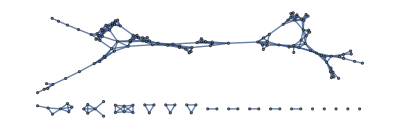
```mathematica
cancer=-Graphics-
```

-Graphics-

```mathematica
cancerOrder={}; (*Taken for Python Files*)
```

```mathematica
cancerA=Graph[Table[If[cancerOrder[[e[[1]]]]>cancerOrder[[e[[2]]]],e[[2]]->e[[1]],e[[1]]->e[[2]]],{e,EdgeList[cancer]}]];
```

```mathematica
paths=kPaths[cancerA,5];
```

```mathematica
SeedRandom[1];
Table[testGraphkIP[cancerA,k,100],{k,3,10}]
```

$Aborted

Cat dataset:

```mathematica
cat=Import["D:\\Programming\\Save\\Thesis\\cat.graph6","Graph6",VertexLabels->"Name"];
```

```mathematica
catOrder={}; (*Taken for Python Files*)
```

```mathematica
catA=Graph[Table[If[catOrder[[e[[1]]]]>catOrder[[e[[2]]]],e[[2]]->e[[1]],e[[1]]->e[[2]]],{e,EdgeList[cat]}]];
```

```mathematica
testGraphkIP[catA,3,100]
```

{seed,n,m,3,100,5,6}

{5,6}

Horse Dataset:

```mathematica
horse=Import["D:\\Programming\\Save\\Thesis\\horse.graph6","Graph6"];
```

```mathematica
horseOrder={};  (*Taken for Python Files*)
```

```mathematica
horseA=Graph[Table[If[horseOrder[[e[[1]]]]>horseOrder[[e[[2]]]],e[[2]]->e[[1]],e[[1]]->e[[2]]],{e,EdgeList[horse]}]];
```

```mathematica
testGraphkIP[horseA,5,100]
```

{seed,n,m,5,100,2,3}

{2,3}

Lion dataset:

```mathematica
lion=Import["D:\\Programming\\Save\\Thesis\\lion.graph6","Graph6"];
```

```mathematica
lionOrder={}; (*Taken for Python Files*)
```

```mathematica
lionA=Graph[Table[If[lionOrder[[e[[1]]]]>lionOrder[[e[[2]]]],e[[2]]->e[[1]],e[[1]]->e[[2]]],{e,EdgeList[lion]}]];
```

```mathematica
testGraphkIP[lionA,3,100]
```

{seed,n,m,3,100,5,6}

{5,6}

The MNIST dataset:

```mathematica
digits=Import["D:\\Programming\\Save\\Thesis\\digits.graph6","Graph6"];
```

```mathematica
digitsOrder={}; (*Taken for Python Files*)
```

```mathematica
catA=Graph[Table[If[catOrder[[e[[1]]]]>catOrder[[e[[2]]]],e[[2]]->e[[1]],e[[1]]->e[[2]]],{e,EdgeList[cat]}]];
```

## Optimization

Some optimizations of testing, not necessary for thesis.

```mathematica
SeedRandom[3];
graph=generateDAG[10,30];
{a,paths}=kPaths[graph,4]//Timing
```

{4.09375,{{1->2,2->3,3->4,4->5},{1->2,2->3,3->4,4->6},{1->2,2->3,3->4,4->7},{1->2,2->3,3->4,4->8},{1->2,2->3,3->4,4->9},{1->2,2->3,3->4,4->10},{1->2,2->3,3->5,5->6},{1->2,2->3,3->5,5->7},{1->2,2->3,3->5,5->10},{1->2,2->3,3->6,6->9},{1->2,2->4,4->5,5->6},{1->2,2->4,4->5,5->7},{1->2,2->4,4->5,5->10},{1->2,2->4,4->6,6->9},{1->2,2->4,4->7,7->8},{1->2,2->4,4->7,7->9},{1->2,2->4,4->7,7->10},{1->3,3->4,4->5,5->6},{1->3,3->4,4->5,5->7},{1->3,3->4,4->5,5->10},{1->3,3->4,4->6,6->9},{1->3,3->4,4->7,7->8},{1->3,3->4,4->7,7->9},{1->3,3->4,4->7,7->10},{1->3,3->5,5->6,6->9},{1->3,3->5,5->7,7->8},{1->3,3->5,5->7,7->9},{1->3,3->5,5->7,7->10},{1->4,4->5,5->6,6->9},{1->4,4->5,5->7,7->8},{1->4,4->5,5->7,7->9},{1->4,4->5,5->7,7->10},{2->3,3->4,4->5,5->6},{2->3,3->4,4->5,5->7},{2->3,3->4,4->5,5->10},{2->3,3->4,4->6,6->9},{2->3,3->4,4->7,7->8},{2->3,3->4,4->7,7->9},{2->3,3->4,4->7,7->10},{2->3,3->5,5->6,6->9},{2->3,3->5,5->7,7->8},{2->3,3->5,5->7,7->9},{2->3,3->5,5->7,7->10},{2->4,4->5,5->6,6->9},{2->4,4->5,5->7,7->8},{2->4,4->5,5->7,7->9},{2->4,4->5,5->7,7->10},{3->4,4->5,5->6,6->9},{3->4,4->5,5->7,7->8},{3->4,4->5,5->7,7->9},{3->4,4->5,5->7,7->10}}}

```mathematica
Clear[kPaths]
kPaths[graph_,k_]:=Select[Tuples[EdgeList[graph],k],CountDistinct[#]==Length[#]&&#⟦All,2⟧⟦1;;-2⟧==#⟦All,1⟧⟦2;;-1⟧&]
```

```mathematica
Clear[kPaths2]
kPaths2[graph_,k_]:=Module[{order=TopologicalSort[graph]},
Map[Partition[#,2,1]&,Flatten[Table[Table[FindPath[graph,order[[i]],order[[j]],{k},Infinity],{i,1,j-1}],{j,2,VertexCount[graph]}],2]]]
```

```mathematica
{a,paths}=kPaths[graph,4]//Timing
{a,paths2}=kPaths2[graph,4]//Timing
```

{3.92188,{{1->2,2->3,3->4,4->5},{1->2,2->3,3->4,4->6},{1->2,2->3,3->4,4->7},{1->2,2->3,3->4,4->8},{1->2,2->3,3->4,4->9},{1->2,2->3,3->4,4->10},{1->2,2->3,3->5,5->6},{1->2,2->3,3->5,5->7},{1->2,2->3,3->5,5->10},{1->2,2->3,3->6,6->9},{1->2,2->4,4->5,5->6},{1->2,2->4,4->5,5->7},{1->2,2->4,4->5,5->10},{1->2,2->4,4->6,6->9},{1->2,2->4,4->7,7->8},{1->2,2->4,4->7,7->9},{1->2,2->4,4->7,7->10},{1->3,3->4,4->5,5->6},{1->3,3->4,4->5,5->7},{1->3,3->4,4->5,5->10},{1->3,3->4,4->6,6->9},{1->3,3->4,4->7,7->8},{1->3,3->4,4->7,7->9},{1->3,3->4,4->7,7->10},{1->3,3->5,5->6,6->9},{1->3,3->5,5->7,7->8},{1->3,3->5,5->7,7->9},{1->3,3->5,5->7,7->10},{1->4,4->5,5->6,6->9},{1->4,4->5,5->7,7->8},{1->4,4->5,5->7,7->9},{1->4,4->5,5->7,7->10},{2->3,3->4,4->5,5->6},{2->3,3->4,4->5,5->7},{2->3,3->4,4->5,5->10},{2->3,3->4,4->6,6->9},{2->3,3->4,4->7,7->8},{2->3,3->4,4->7,7->9},{2->3,3->4,4->7,7->10},{2->3,3->5,5->6,6->9},{2->3,3->5,5->7,7->8},{2->3,3->5,5->7,7->9},{2->3,3->5,5->7,7->10},{2->4,4->5,5->6,6->9},{2->4,4->5,5->7,7->8},{2->4,4->5,5->7,7->9},{2->4,4->5,5->7,7->10},{3->4,4->5,5->6,6->9},{3->4,4->5,5->7,7->8},{3->4,4->5,5->7,7->9},{3->4,4->5,5->7,7->10}}}

{0.,{{{1,2},{2,3},{3,4},{4,5}},{{1,3},{3,4},{4,5},{5,7}},{{1,2},{2,4},{4,5},{5,7}},{{1,2},{2,3},{3,5},{5,7}},{{1,2},{2,3},{3,4},{4,7}},{{2,3},{3,4},{4,5},{5,7}},{{1,4},{4,5},{5,7},{7,10}},{{1,3},{3,5},{5,7},{7,10}},{{1,3},{3,4},{4,7},{7,10}},{{1,3},{3,4},{4,5},{5,10}},{{1,2},{2,4},{4,7},{7,10}},{{1,2},{2,4},{4,5},{5,10}},{{1,2},{2,3},{3,5},{5,10}},{{1,2},{2,3},{3,4},{4,10}},{{2,4},{4,5},{5,7},{7,10}},{{2,3},{3,5},{5,7},{7,10}},{{2,3},{3,4},{4,7},{7,10}},{{2,3},{3,4},{4,5},{5,10}},{{3,4},{4,5},{5,7},{7,10}},{{1,4},{4,5},{5,7},{7,8}},{{1,3},{3,5},{5,7},{7,8}},{{1,3},{3,4},{4,7},{7,8}},{{1,2},{2,4},{4,7},{7,8}},{{1,2},{2,3},{3,4},{4,8}},{{2,4},{4,5},{5,7},{7,8}},{{2,3},{3,5},{5,7},{7,8}},{{2,3},{3,4},{4,7},{7,8}},{{3,4},{4,5},{5,7},{7,8}},{{1,3},{3,4},{4,5},{5,6}},{{1,2},{2,4},{4,5},{5,6}},{{1,2},{2,3},{3,5},{5,6}},{{1,2},{2,3},{3,4},{4,6}},{{2,3},{3,4},{4,5},{5,6}},{{1,4},{4,5},{5,7},{7,9}},{{1,4},{4,5},{5,6},{6,9}},{{1,3},{3,5},{5,7},{7,9}},{{1,3},{3,5},{5,6},{6,9}},{{1,3},{3,4},{4,7},{7,9}},{{1,3},{3,4},{4,6},{6,9}},{{1,2},{2,4},{4,7},{7,9}},{{1,2},{2,4},{4,6},{6,9}},{{1,2},{2,3},{3,6},{6,9}},{{1,2},{2,3},{3,4},{4,9}},{{2,4},{4,5},{5,7},{7,9}},{{2,4},{4,5},{5,6},{6,9}},{{2,3},{3,5},{5,7},{7,9}},{{2,3},{3,5},{5,6},{6,9}},{{2,3},{3,4},{4,7},{7,9}},{{2,3},{3,4},{4,6},{6,9}},{{3,4},{4,5},{5,7},{7,9}},{{3,4},{4,5},{5,6},{6,9}}}}

```mathematica
Flatten[Table[Table[FindPath[graph,order[[i]],order[[j]],{4},Infinity],{i,1,j-1}],{j,2,10}],2]
```

{{1,2,3,4,5},{1,3,4,5,7},{1,2,4,5,7},{1,2,3,5,7},{1,2,3,4,7},{2,3,4,5,7},{1,4,5,7,10},{1,3,5,7,10},{1,3,4,7,10},{1,3,4,5,10},{1,2,4,7,10},{1,2,4,5,10},{1,2,3,5,10},{1,2,3,4,10},{2,4,5,7,10},{2,3,5,7,10},{2,3,4,7,10},{2,3,4,5,10},{3,4,5,7,10},{1,4,5,7,8},{1,3,5,7,8},{1,3,4,7,8},{1,2,4,7,8},{1,2,3,4,8},{2,4,5,7,8},{2,3,5,7,8},{2,3,4,7,8},{3,4,5,7,8},{1,3,4,5,6},{1,2,4,5,6},{1,2,3,5,6},{1,2,3,4,6},{2,3,4,5,6},{1,4,5,7,9},{1,4,5,6,9},{1,3,5,7,9},{1,3,5,6,9},{1,3,4,7,9},{1,3,4,6,9},{1,2,4,7,9},{1,2,4,6,9},{1,2,3,6,9},{1,2,3,4,9},{2,4,5,7,9},{2,4,5,6,9},{2,3,5,7,9},{2,3,5,6,9},{2,3,4,7,9},{2,3,4,6,9},{3,4,5,7,9},{3,4,5,6,9}}

```mathematica
Map[Partition[#,2,1]&,Flatten[Table[Table[FindPath[graph,order[[i]],order[[j]],{4},Infinity],{i,1,j-1}],{j,2,10}],2]]
```

{{{1,2},{2,3},{3,4},{4,5}},{{1,3},{3,4},{4,5},{5,7}},{{1,2},{2,4},{4,5},{5,7}},{{1,2},{2,3},{3,5},{5,7}},{{1,2},{2,3},{3,4},{4,7}},{{2,3},{3,4},{4,5},{5,7}},{{1,4},{4,5},{5,7},{7,10}},{{1,3},{3,5},{5,7},{7,10}},{{1,3},{3,4},{4,7},{7,10}},{{1,3},{3,4},{4,5},{5,10}},{{1,2},{2,4},{4,7},{7,10}},{{1,2},{2,4},{4,5},{5,10}},{{1,2},{2,3},{3,5},{5,10}},{{1,2},{2,3},{3,4},{4,10}},{{2,4},{4,5},{5,7},{7,10}},{{2,3},{3,5},{5,7},{7,10}},{{2,3},{3,4},{4,7},{7,10}},{{2,3},{3,4},{4,5},{5,10}},{{3,4},{4,5},{5,7},{7,10}},{{1,4},{4,5},{5,7},{7,8}},{{1,3},{3,5},{5,7},{7,8}},{{1,3},{3,4},{4,7},{7,8}},{{1,2},{2,4},{4,7},{7,8}},{{1,2},{2,3},{3,4},{4,8}},{{2,4},{4,5},{5,7},{7,8}},{{2,3},{3,5},{5,7},{7,8}},{{2,3},{3,4},{4,7},{7,8}},{{3,4},{4,5},{5,7},{7,8}},{{1,3},{3,4},{4,5},{5,6}},{{1,2},{2,4},{4,5},{5,6}},{{1,2},{2,3},{3,5},{5,6}},{{1,2},{2,3},{3,4},{4,6}},{{2,3},{3,4},{4,5},{5,6}},{{1,4},{4,5},{5,7},{7,9}},{{1,4},{4,5},{5,6},{6,9}},{{1,3},{3,5},{5,7},{7,9}},{{1,3},{3,5},{5,6},{6,9}},{{1,3},{3,4},{4,7},{7,9}},{{1,3},{3,4},{4,6},{6,9}},{{1,2},{2,4},{4,7},{7,9}},{{1,2},{2,4},{4,6},{6,9}},{{1,2},{2,3},{3,6},{6,9}},{{1,2},{2,3},{3,4},{4,9}},{{2,4},{4,5},{5,7},{7,9}},{{2,4},{4,5},{5,6},{6,9}},{{2,3},{3,5},{5,7},{7,9}},{{2,3},{3,5},{5,6},{6,9}},{{2,3},{3,4},{4,7},{7,9}},{{2,3},{3,4},{4,6},{6,9}},{{3,4},{4,5},{5,7},{7,9}},{{3,4},{4,5},{5,6},{6,9}}}